```mathematica
Use Logistic Distribution to Simulate Fractional Change
```

```mathematica
sp500=FinancialData["SP500","FractionalChange",{{2000,1,1},{2009,1,1},"Day"}];
```

```mathematica
edist=EstimatedDistribution[sp500[[All,2]],LogisticDistribution[μ,β]];
```

-Graphics-

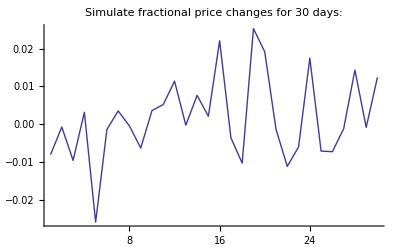

```mathematica
Show[Histogram[sp500[[All,2]],{-0.05,0.13,0.005},"PDF",PlotRange->{0,60},ChartStyle->"Pastel"],Plot[PDF[edist,x],{x,-0.1,0.12},PlotStyle->{Thick,Black},PlotRange->All],BaseStyle->{FontFamily->"Verdana"},ImageSize->430,Epilog->Inset[Framed[Style[Grid[{{"Estimated distribution: "},{Round[#,0.000001]&/@edist}}],11,FontFamily->"Verdana"],Background->LightBlue,RoundingRadius->3],{Right,Top},{Right,Top}]]

ListPlot[RandomVariate[edist,30],Joined->True,PlotStyle->Thick,ImageSize->400,BaseStyle->{FontFamily->"Verdana"},PlotLabel->"Simulate fractional price changes for 30 days:"]
```